### Premice in ravnine

Premica v 2D podana z dvema točkama.

```mathematica
p = Daljica[{0, 4}, {3, 1}]
```

Daljica[{0,4},{3,1}]

```mathematica
Slika[Daljica[AA_, BB_]] := Line[{AA, BB}]
```

```mathematica
Slika[p]
```

Line[{{0,4},{3,1}}]

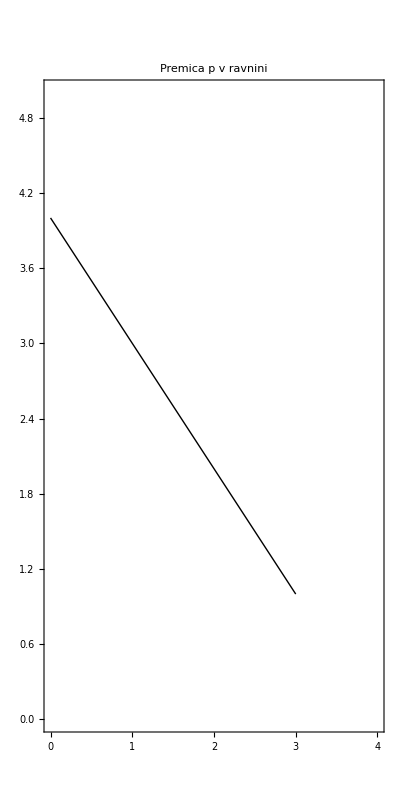

```mathematica
Risba = Graphics[Slika[p], PlotRange->{{0, 4}, {0, 5}}, Axes->True, Frame->True, AspectRatio->2/1, PlotLabel->"Premica p v ravnini"]
```

```mathematica
EnacbaPremice[Daljica[AA_, BB_]] := Module[{x1, y1, x2, y2, k, n}, 
{x1, y1} = AA;
{x2, y2} = BB;
k = (y2-y1)/(x2-x1);
n = n /. First[Solve[y1 == x1 * k + n, n]];
y == k * x + n]
```

```mathematica
EnacbaPremice[p]
```

y==4-x

```mathematica
Premica1 = EnacbaPremice[p]
```

y==4-x

```mathematica
ClearAll[Premica]
```

```mathematica
y = -x + 4
```

4-x

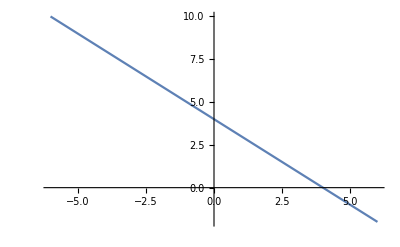

```mathematica
Plot[y, {x, -6, 6}]
```

```mathematica
Manipulate[Plot[k x + n, {x, -8, 8}, PlotRange->{-8, 8}], {k, -3, 3}, {n, -3, 3}]
```